```mathematica
Numerical solution to problem 2.9 from ' Statics and Strength of Materials' 3 rd, Bassin, Brodsky, Wolkoff.

Generate diagrams for these sorts of problems.
```

```mathematica
<<peeters`
peeters`setGitDir["../project/figures/GAelectrodynamics"]
```

peeters`

/Users/pjoot/project/figures/GAelectrodynamics

```mathematica
ClearAll[t, a, b, fr, fs]

fr[alpha_, beta_, mg_] := - mg Sin[beta]/Sin[beta - alpha]
fs[alpha_, beta_, mg_] :=  mg Sin[alpha]/Sin[beta - alpha]
t = ArcSin[2/6.5]
a = 2 t
b = Pi/2 + t

{t,a,b} 180/Pi
```

9.8

0.312767

0.625533

1.88356

{17.9202,35.8404,107.92}

```mathematica
ClearAll[mm]
mm = 1000;
fs[a, b, mm * 9.8]
fr[a,b,mm * 9.8]
```

59101.5

-96040.

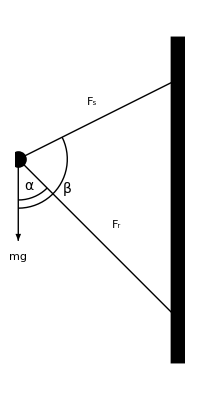

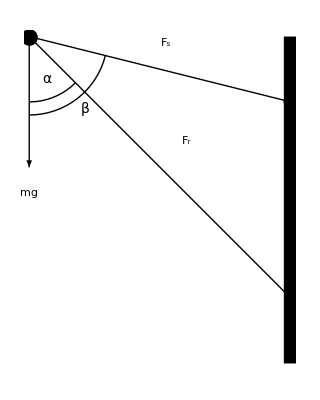

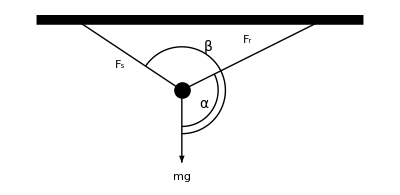

```mathematica
ClearAll[zToVector, mgi, fri, fsi, o, bf, sf, argdiff, g1, g2, g3, o, diagram]

zToVector := { #// Re, # // Im} &;
bf := Style[#, {FontSize->14, Bold}] &;
sf := Style[#, {FontSize->14}] &;
o = 0 // zToVector;
argdiff[z2_, z1_] := Module[ {a,b}, b = z2/Norm[z2];a = z1/Norm[z1];Arg[z2/z1]]

Options[diagram]={ah->0.1,th-> 0.05, betashift -> 0};
diagram[mgi_, fri_, fsi_, alpha_, beta_, line_, OptionsPattern[]] := Module[{mg,fr,fs},
mg = mgi// zToVector;
fr =fri // zToVector;
fs = fsi // zToVector;

Graphics[{
Thick,
Arrowheads[OptionValue@ah],
Arrow[{o,mg}],
Arrow[{o,fr}],
Arrow[{o,fs}],
PointSize[0.03],
Point[o],
Text[Row[{"m" // sf, "g"//bf}], 1.2 * mg] ,
Text[Subscript["F" // bf, "s" //sf], fs/2 + (0.1 * fsi * I// zToVector)],
Text[Subscript["F" // bf, "r" //sf], fr/2 + (0.1 * fri * I// zToVector)],
Circle[o,1, {-Pi/2, -Pi/2 + alpha}],
Circle[o,1.2, {-Pi/2, -Pi/2 + beta}],
Text["α"// sf, 0.7 * mgi * E^(I alpha/2)/Norm[mgi] // zToVector],
Text["β"// sf, 1.4 * mgi * E^(I (beta + OptionValue@betashift)/2)/Norm[mgi] // zToVector],
Thickness[OptionValue@th],
Line[line]
}]
]

mgi = -2 I ;
fri = 4 - 4 I;
fsi = 4 + 2I;
g1 =diagram[ mgi, fri, fsi, argdiff[fri, mgi],  argdiff[fsi, mgi],{{4,3}, {4,-5}}, th-> 0.04]


mgi = -2 I ;
fri = 4 - 4 I;
fsi = 4 - I;
g2 = diagram[ mgi, fri, fsi, argdiff[fri, mgi],  argdiff[fsi, mgi],{{4,0}, {4,-5}}, th-> 0.025, ah ->0.07]


mgi = -2 I ;
fri = 4 + 2I;
fsi = -3 +2 I;
g3 = diagram[ mgi, fri, fsi, argdiff[fri, mgi],  argdiff[fsi, mgi] + 2 Pi,{{-4, 2}, {5, 2}}, ah ->0.05, th-> 0.025, betashift -> Pi/3]
```

```mathematica
peeters`exportForLatex["twoForceProblemWithWeightFigure1",g1]
peeters`exportForLatex["twoForceProblemWithWeightFigure2",g2]
peeters`exportForLatex["twoForceProblemWithWeightFigure3",g3]
```

{twoForceProblemWithWeightFigure1.eps,twoForceProblemWithWeightFigure1pn.png}

{twoForceProblemWithWeightFigure2.eps,twoForceProblemWithWeightFigure2pn.png}

{twoForceProblemWithWeightFigure3.eps,twoForceProblemWithWeightFigure3pn.png}